# Learning XOR

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

```mathematica
HardNOTImpl[Table[{True,False,True},4],{{True,True,True},{False,False,True},{False,True,True},{True,False,True}}]
```

{!neurallogic`Private`f[{True,False,True},{True,True,True}],!neurallogic`Private`f[{True,False,True},{False,False,True}],!neurallogic`Private`f[{True,False,True},{False,True,True}],!neurallogic`Private`f[{True,False,True},{True,False,True}]}

```mathematica
Outer[f,{True,False,True},{{True,True,True},{False,False,True},{False,True,True},{True,False,True}},Not]
```

Outer[f,{True,False,True},{{True,True,True},{False,False,True},{False,True,True},{True,False,True}},Not]

## Get data

```mathematica
numBooleanVariables=10; (* 2^numBooleanVariables possible inputs *)
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10]&,"BooleanFunction"];
maxExamples=Min[2000,2^numBooleanVariables];
numClasses=2;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->bf@@x]&,Range[maxExamples]];
```

```mathematica
Take[examples,3]
```

{{1.,0.,1.,1.,0.,1.,1.,0.,1.,0.}→False,{1.,1.,1.,0.,0.,0.,1.,0.,1.,1.}→False,{1.,1.,1.,1.,0.,0.,1.,0.,0.,0.}→True}

```mathematica
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
targetEncoder=NetEncoder[{"Class",{True,False},"IndicatorVector"}];
```

## Create net

```mathematica
{softNet,hardNet}=With[{classificationLayerSize=8*numClasses},
HardNeuralChain[{
HardNeuralMajority[inputSize,50],
HardDropoutLayer[0.25],
HardNeuralMajority[50,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{softNet,hardNet}=With[{classificationLayerSize=16*numClasses},
HardNeuralChain[{
HardNeuralMajority[inputSize,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
trainableSoftNet=NetGraph[<|"NeuralLogicNet"->softNet,"Loss"->HardClassificationLoss[]|>,{"NeuralLogicNet"->"Loss"},"Target"->targetEncoder];
```

```mathematica
trainableSoftNet
```

NetGraph[<>]

## Train net

```mathematica
result=NetTrain[trainableSoftNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,{},
"Output"->NetDecoder[targetEncoder]]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]
]};
```

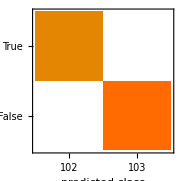
{Classifier Measurements
Classifier method | Net
Number of test examples | 205
Accuracy | (100.00000000000000022) %
Accuracy baseline | (50.23.5) %
Geometric mean of probabilities | 0.948 ± 0.0052
Mean cross entropy | 0.0531 ± 0.0055
Single evaluation time | 1.68 ms/example
Batch evaluation speed | 4.97 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 205
Accuracy | (100.00000000000000022) %
Accuracy baseline | (50.23.5) %
Geometric mean of probabilities | 0.948 ± 0.0052
Mean cross entropy | 0.0531 ± 0.0055
Single evaluation time | 2.02 ms/example
Batch evaluation speed | 11.5 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData]&/@{trainedSoftNet,trainedHardNet}
```

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedHardNet];
```

```mathematica
hncwt=HardNetClassify[hnf,testData,NetDecoder[targetEncoder],First[#]&,Last[#]&];
```

```mathematica
eval=HardNetClassifyEvaluation[hncwt];
eval["Accuracy"]
```

0.639024

```mathematica
hncwt2=Association[{"Prediction"->trainedHardNet[First[#]],"Target"->Last[#]}]&/@testData;
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

1.

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

0.0390625 kB

```mathematica
HardNetBooleanExpression[hnf,inputSize];
```

## Train standard net

```mathematica
classifier=Classify[trainData->"Target",Method->"NeuralNetwork",PerformanceGoal->{"Memory","Quality"}]
```

ClassifierFunction[…]

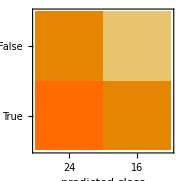
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 40
Accuracy | (55.8.) %
Accuracy baseline | (60.8.) %
Geometric mean of probabilities | 0.464 ± 0.038
Mean cross entropy | 0.768 ± 0.081
Single evaluation time | 4.81 ms/example
Batch evaluation speed | 518. examples/s
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[classifier,testData->"Target"]
```

```mathematica
(First@classifier)["Model"]["Network"]
```

NetChain[<>]

```mathematica
Information[classifier,"FunctionMemory"]
```

290. kB